## Mitotic Oscilator in fission yeast (Novak/Tyson)

Reference
Novak B, Tyson JJ (1997)  "Modeling the control of DNA replication in fission yeast , Proc. Natl. Acad. Sci. USA, Vol. 94, pp. 9147–9152, August 1997
 http://www.pnas.org/cgi/content/abstract/94/17/9147

xCellerator implementation
Created: 12 Aug 2005 BES
Revised: 15 Oct 2007 BES - Verify under version 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:17:39.445698 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
auxRules = {
MPF-> G2K[t]+β*PG2[t],
SPF-> G2K[t]+β*PG2[t]+α*G1K[t]+Cig1};
rateRules={
k2-> V2p*(1-UbE[t])+V2*UbE[t],
k25-> V25p*(1-Cdc25[t])+V25*Cdc25[t],
k6-> V6p*(1-UbE2[t])+V6*UbE2[t],
kwee-> Vwp*(1-Wee1[t])+Vw*Wee1[t]
};
```

```mathematica
stn={
{∅->mass,  μ mass[t]},

{∅⇄G2K,k1,k2},
{∅⇄R,k3,k4},
{G2K⇄PG2, kwee, k25},
{R+G2K⇄G2R, k7, k7r},
{R+PG2⇄PG2R, k7, k7r},
{(R↦∅)^mass,hill[1, Kmp, 1, 0, kp*SPF]},
{G2R->G2K,k4},
{PG2->∅,k2},
{G2R->R,k2+k2p},
{PG2R->R,k2+k2p},
{PG2R->PG2,k4},


{G1R->G1K,k4},
{∅⇄G1K, k5,k6},
{R+G1K⇄G1R,k8,k8r},
{G1R->R, k6p},

{IE↦∅,hill[1, Kmir, 1,0, kir]},
{IEC↦IE, hill[1, Kmi, 1, 0, ki*MPF]},

{UbE↦∅,hill[1,Kmur, 1, 0,  kur]},
{UbEC↦UbE, hill[1,Kmu,1,0,ku IE[t]]},

{UbE2↦∅,hill[1, Kmur2,1,0,kur2]},

{UbE2C↦UbE2, hill[1, Kmu2, 1, 0, ku2*MPF]},

{Wee1↦∅, hill[1, Kmw, 1, 0,  kw*MPF]}, 
{Wee1C↦Wee1, hill[1, Kmwr, 1, 0, kwr]},

{Cdc25 ↦∅, hill[1,Kmcr, 1,0,  kcr]},

{Cdc25C↦Cdc25,hill[1,Kmc,1,0,  kc*MPF]}
}/.auxRules/.rateRules;
```

```mathematica
rc={UbEC[t]-> 1-UbE[t],
IEC[t]-> 1-IE[t],
UbE2C[t]-> 1-UbE2[t],
Wee1C[t]-> 1-Wee1[t],
Cdc25C[t] -> 1-Cdc25[t],
k1->  0.015, 
k3 ->  0.09375,
k2p->  0.05,
k4 ->  0.1875,
k5 ->  0.00175,
k7 ->  100,
k7r-> 0.1,
k6p-> 0,
k8 ->  10,
k8r ->  0.1,
kp ->  3.25,

ki-> 0.4,
Kmi ->  0.01,
kir ->  0.1,
Kmir ->  0.01,
kur ->  0.1,
Kmur ->  0.01,
ku-> 0.2,
Kmu-> 0.01,
kur2-> 0.3,
Kmur2-> 0.05,
ku2-> 1,
Kmu2-> 0.05,
kwr ->  0.25,
Kmwr-> 0.1,
kw-> 1,
Kmw-> 0.1,
kcr ->  0.25,
Kmcr-> 0.1,
kc-> 1,
Kmc-> 0.1,

Kmp-> 0.001,

V2 ->  0.25,
V2p-> 0.0075,
V25 ->  0.5,
V25p-> 0.025,
V6 ->  7.5,
V6p-> 0.0375,
Vw-> 0.35,
Vwp ->   0.035,


α-> 0.25,
β-> 0.05,
μ-> 0.00495,

Cig1-> 0};
```

```mathematica
sys=interpret[stn]/.rc
```

{{Cdc25'[t]==-(0.25 Cdc25[t])/(0.1+Cdc25[t])+((1-Cdc25[t]) (G2K[t]+0.05 PG2[t]))/(1.1-Cdc25[t]),G1K'[t]==0.00175+0.2875 G1R[t]-10 G1K[t] R[t]-G1K[t] (0.0375 (1-UbE2[t])+7.5 UbE2[t]),G1R'[t]==-0.2875 G1R[t]+10 G1K[t] R[t],G2K'[t]==0.015+0.2875 G2R[t]+(0.025 (1-Cdc25[t])+0.5 Cdc25[t]) PG2[t]-100 G2K[t] R[t]-G2K[t] (0.0075 (1-UbE[t])+0.25 UbE[t])-G2K[t] (0.035 (1-Wee1[t])+0.35 Wee1[t]),G2R'[t]==-0.2875 G2R[t]+100 G2K[t] R[t]-G2R[t] (0.05+0.0075 (1-UbE[t])+0.25 UbE[t]),IE'[t]==-(0.1 IE[t])/(0.01+IE[t])+(0.4 (1-IE[t]) (G2K[t]+0.05 PG2[t]))/(1.01-IE[t]),mass'[t]==0.00495 mass[t],PG2'[t]==-(0.025 (1-Cdc25[t])+0.5 Cdc25[t]) PG2[t]+0.2875 PG2R[t]-100 PG2[t] R[t]-PG2[t] (0.0075 (1-UbE[t])+0.25 UbE[t])+G2K[t] (0.035 (1-Wee1[t])+0.35 Wee1[t]),PG2R'[t]==-0.2875 PG2R[t]+100 PG2[t] R[t]-PG2R[t] (0.05+0.0075 (1-UbE[t])+0.25 UbE[t]),R'[t]==0.09375+0.1 G1R[t]+0.1 G2R[t]+0.1 PG2R[t]-0.1875 R[t]-10 G1K[t] R[t]-100 G2K[t] R[t]-100 PG2[t] R[t]-(3.25 mass[t] (0.25 G1K[t]+G2K[t]+0.05 PG2[t]) R[t])/(0.001+R[t])+G2R[t] (0.05+0.0075 (1-UbE[t])+0.25 UbE[t])+PG2R[t] (0.05+0.0075 (1-UbE[t])+0.25 UbE[t]),UbE'[t]==(0.2 IE[t] (1-UbE[t]))/(1.01-UbE[t])-(0.1 UbE[t])/(0.01+UbE[t]),UbE2'[t]==((G2K[t]+0.05 PG2[t]) (1-UbE2[t]))/(1.05-UbE2[t])-(0.3 UbE2[t])/(0.05+UbE2[t]),Wee1'[t]==(0.25 (1-Wee1[t]))/(1.1-Wee1[t])-((G2K[t]+0.05 PG2[t]) Wee1[t])/(0.1+Wee1[t])},{Cdc25,G1K,G1R,G2K,G2R,IE,mass,PG2,PG2R,R,UbE,UbE2,Wee1}}

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Cdc25,G1K,G1R,G2K,G2R,IE,PG2,PG2R,R,UbE,UbE2,Wee1}

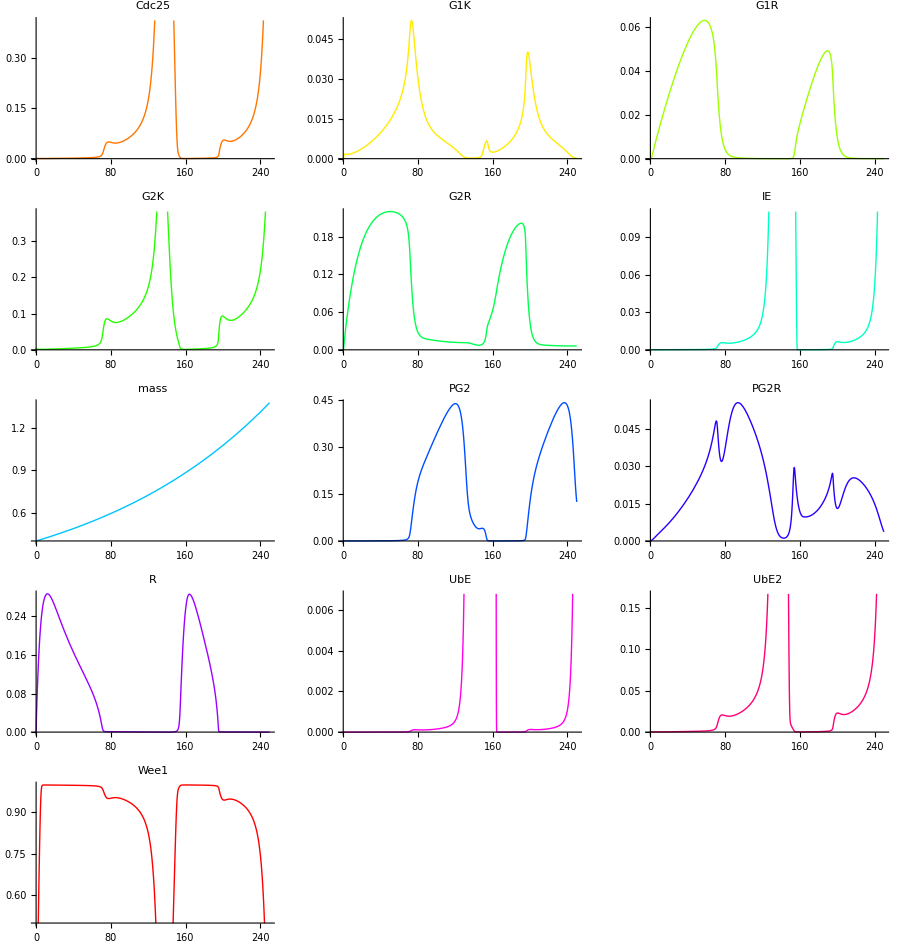

{{Cdc25→InterpolatingFunction[{{0.,250.}},<>],G1K→InterpolatingFunction[{{0.,250.}},<>],G1R→InterpolatingFunction[{{0.,250.}},<>],G2K→InterpolatingFunction[{{0.,250.}},<>],G2R→InterpolatingFunction[{{0.,250.}},<>],IE→InterpolatingFunction[{{0.,250.}},<>],mass→InterpolatingFunction[{{0.,250.}},<>],PG2→InterpolatingFunction[{{0.,250.}},<>],PG2R→InterpolatingFunction[{{0.,250.}},<>],R→InterpolatingFunction[{{0.,250.}},<>],UbE→InterpolatingFunction[{{0.,250.}},<>],UbE2→InterpolatingFunction[{{0.,250.}},<>],Wee1→InterpolatingFunction[{{0.,250.}},<>]}}

```mathematica
sim=run[sys,
timeSpan->250,
initialConditions-> {mass-> 0.4}, ImageSize-> 900,
gridPlotVariables-> All,plot-> True, plotVariables-> None,
MaxSteps-> 25000]
```

```mathematica
plotFunctions= {
{MPF,G2K[t]+β*PG2[t]},
{SPF,G2K[t]+β*PG2[t]+α*G1K[t]+Cig1},
{Rum1,R[t]+G1R[t]+G2R[t]+PG2R[t]},
{Cdc13,G2K[t]+G2R[t]+PG2[t]+PG2R[t]},
{Cig2, G1K[t]+G1R[t]}
}/.rc
```

{{MPF,G2K[t]+0.05 PG2[t]},{SPF,0.25 G1K[t]+G2K[t]+0.05 PG2[t]},{Rum1,G1R[t]+G2R[t]+PG2R[t]+R[t]},{Cdc13,G2K[t]+G2R[t]+PG2[t]+PG2R[t]},{Cig2,G1K[t]+G1R[t]}}

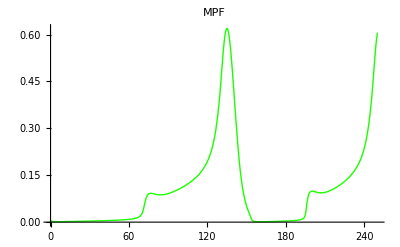
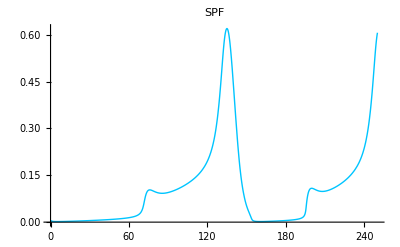
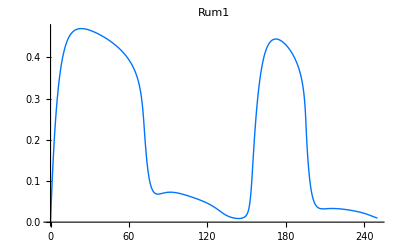
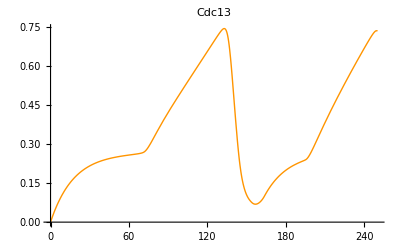
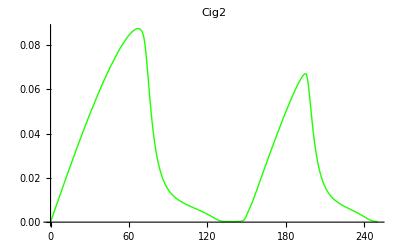

```mathematica
Plot[Evaluate[#[[2]]/.sim], {t,0,250},PlotLabel-> #[[1]], PlotRange-> All, PlotStyle-> Hue[Random[Real,{0,1}]]]&/@plotFunctions
```